```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/pyBBN/tests/matter-rad_equality_photon-electron-neutrino_universe

### Parcing log.txt file

```mathematica
lines = Import["./output/evolution.txt", {"Text", "Lines"}][[2;; ]];
lines = StringSplit/@lines;
lines = Map[Read[StringToStream[#],Number]&, lines, {2}];
```

```mathematica
cols= Transpose@lines;
```

```mathematica
tdat=lines[[All,5]];
Tdat=lines[[All,2]];
ρdat=lines[[All,6]];
adat=lines[[All,3]];
aTdat=lines[[All,1]];
Neffdat=lines[[All,7]];
```

### Genelar constants

```mathematica
gg =2+7/8*(4+6);
Mpl=1.220910 * 10^22/(1.66 √gg) (*MeV*);
G=(10^-22/1.220910)^2;
```

```mathematica
MevToSec=6.5821220 10^-22 (*Converts Mev^-1 to sec*);
```

```mathematica
me=0.511(*MeV*);
```

```mathematica
ge=4;
gγ=2;
```

```mathematica
T0=100(*MeV*);
```

### Some basic definitions

```mathematica
fFermi[p_,T_,m_]:=1/(ⅇ^((√(p^2+m^2))/T)+1)
fFermiNonrel[p_,T_,m_]:=ⅇ^(-(m+p^2/2m)/T)
```

```mathematica
ρFermi[T_,m_,gf_]:=gf NIntegrate[(4 π)/(2π)^3 fFermi[p,T,m] p^2 √(p^2+m^2),{p,0,∞}]
```

## Matter-radiation equality

```mathematica
Tdec=10;
```

```mathematica
nedec=4(4 π)/(2π)^3 NIntegrate[p^2 fFermi[p,Tdec,me],{p,0,∞}];
```

```mathematica
ne[T_]:=nedec (T/Tdec)^3
```

```mathematica
ρrad[T_]:=(2+7/8*6)*π^2/30 T^4
```

```mathematica
ρmatter[T_]:=4  NIntegrate[(4 π)/(2π)^3 fFermi[p,T,0] p^2 √(p^2+me^2),{p,0,∞}]
ρmatter1[T_]:=4  NIntegrate[(4 π)/(2π)^3 fFermi[p,T,me] p^2 √(p^2+me^2),{p,0,∞}]
ρmatterNonrel[T_]:=me ne[T]+3/2 ne[T]T
```

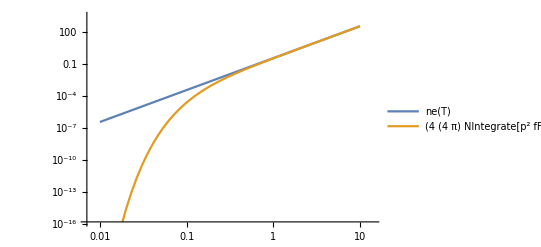

```mathematica
LogLogPlot[{ne[T],4(4 π)/(2π)^3 NIntegrate[p^2 fFermi[p,T,me],{p,0,∞}]},{T,0.01,10},PlotLegends->"Expressions"]
```

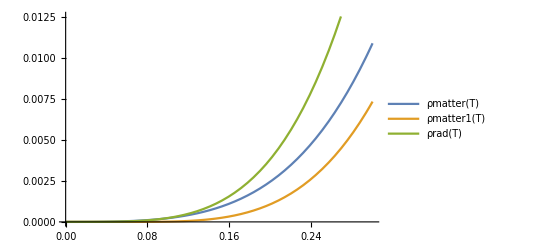

```mathematica
Plot[{ρmatter[T],ρmatter1[T],ρrad[T]},{T,0,0.3},PlotLegends->"Expressions"]
```

```mathematica
LogLogPlot[{ ρmatterNonrel[T],ρrad[T]},{T,0.01,5},,GridLines-> {{1},{}},PlotLegends->"Expressions"]
```

LogLogPlot[{ρmatterNonrel[T],ρrad[T]},{T,0.01,5},Null,GridLines→{{1},{}},PlotLegends→Expressions]

```mathematica
Teq=FindRoot[ρmatterNonrel[T]-ρrad[T]==0,{T,1}][[1,2]]
```

0.101568

## Energy density from scale factor

### Some calculation

ρ=const* a^-4=ρ0 a0^4* a^-4
a0=1/T0
ρ0=π^2/30 g* T0^4*10^24
const=ρ0 a0^4=π^2/30 g*
factor 10^24 appears due to MeV^4→ eV^4 convertation

```mathematica
constρ=π^2/30 gg*10^24//N
```

3.53661×10^24

### Comparing data and analytical solution

```mathematica
ρadat=Transpose[{adat,ρdat}];
```

```mathematica
ρtdat=Transpose[{tdat,ρdat}];
```

```mathematica
ρafitcurve=Fit[ρadat[[;;140]],{a^-4},a];
```

```mathematica
ρafitcurveCOLD=Fit[ρadat[[165;;]],{a^-3},a];
```

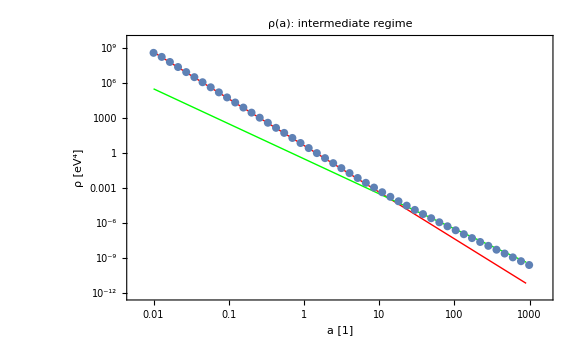

```mathematica
Show[{LogLogPlot[ρafitcurve,{a,0.01,900},GridLines->{{10},{}}, PlotStyle->{Red,Thick}],LogLogPlot[ρafitcurveCOLD,{a,0.01,900},PlotStyle->{Green,Thick}],ListLogLogPlot[ρadat[[;; ;;5]],PlotStyle-> PointSize[0.01],PlotRange->{{0.1,700},Automatic}]},PlotLabel->Style[#,Bold,15]&/@{"ρ(a): intermediate regime"},Frame-> True, FrameLabel->{"a [1]","ρ [eV^4]"}, Ticks->Automatic,Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Radiation: " @ρafitcurve}],LineLegend[{Green},{" Matter: " @ρafitcurveCOLD}]}]],Bold,10],Scaled[{0.46,0.43}],Scaled[{1,1}]], ImageSize-> Large]
```

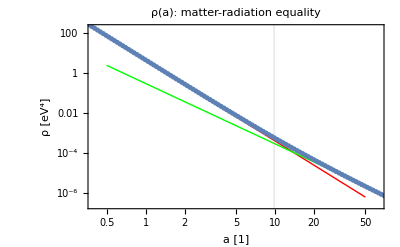

```mathematica
Show[LogLogPlot[ρafitcurve,{a,0.5,50},GridLines->{{1/Teq},{}}, PlotStyle->{Red,Thick}],LogLogPlot[ρafitcurveCOLD,{a,0.5,50},PlotStyle->{Green,Thick},GridLines-> {{10},{}}],ListLogLogPlot[ρadat,PlotRange->{{0.5,50},Automatic}],PlotLabel->Style[#,Bold,15]&/@{"ρ(a): matter-radiation equality"},Frame-> True, FrameLabel->{"a [1]","ρ [eV^4]"}]
```

## Scale factor from time

### Some calculations

a = const* √t=a0 √(t/t0)
t0=1/(2H0)=Mpl^*/(2 T0^2)

```mathematica
t0=Mpl/(2 T0^2)MevToSec
```

0.0000738256

```mathematica
teq=Mpl/(2 Teq^2)MevToSec*√(gg/(2+7/8 6))
```

87.1425

```mathematica
a0 = 1/T0
```

1/100

```mathematica
const=a0/(√t0)
```

1.16385

```mathematica
TT[t_]:=√((Mpl MevToSec)/(2 t))
```

### Alternative calculation

```mathematica
ρ0=π^2/30 gg T0^4
```

(107500000 π^2)/3

```mathematica
t02=√(3/(32 π G ρ0))MevToSec
```

0.0000738188

### Plots

```mathematica
atdat = Transpose[{tdat, adat}];
```

```mathematica
atfitcurve=Fit[atdat[[;;140]],{t^(1/2)},t];
```

```mathematica
atfitcurveCOLD=Fit[atdat[[165 ;;]],{t^(2/3)},t];
```

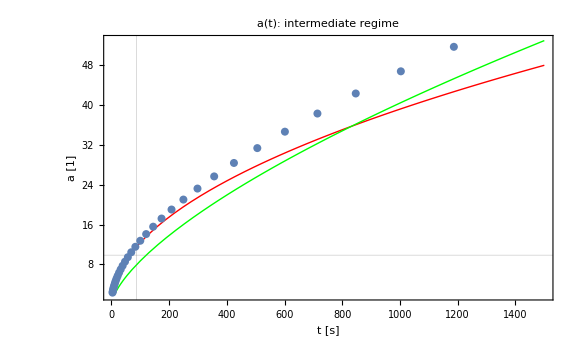

```mathematica
Show[Plot[atfitcurve,{t,3,1500},GridLines->{{teq},{1/Teq}},PlotStyle->{Red,Thick}],Plot[atfitcurveCOLD,{t,10,1500},PlotStyle->{Green,Thick}],ListPlot[atdat[[110;;172 ;; 2]],PlotStyle-> PointSize[0.01],PlotRange->{{10,20},{0.001,0.002}}],PlotLabel->Style[#,Bold,15]&/@{"a(t): intermediate regime"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{"Radiation: " @NumberForm[atfitcurve,4]}],LineLegend[{Green},{"Matter: " @NumberForm[atfitcurveCOLD,4]}]}]],Bold,10],Scaled[{0.97,0.4}],Scaled[{1,1}]],PlotRange-> All,ImageSize-> Large]
```

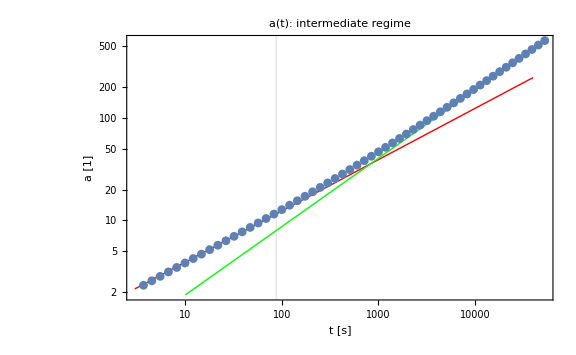

```mathematica
Show[LogLogPlot[atfitcurve,{t,3,40000},GridLines->{{teq},{}},PlotStyle->{Red,Thick}],LogLogPlot[atfitcurveCOLD,{t,10,40000},PlotStyle->{Green,Thick}],ListLogLogPlot[atdat[[110;;220 ;; 2]],PlotRange->{{10,20},{0.001,0.002}}],PlotLabel->Style[#,Bold,15]&/@{"a(t): intermediate regime"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{"Radiation: " @NumberForm[atfitcurve,4]}],LineLegend[{Green},{"Matter: " @NumberForm[atfitcurveCOLD,4]}]}]],Bold,10],Scaled[{0.37,0.96}],Scaled[{1,1}]],PlotRange-> All,ImageSize-> Large]
```

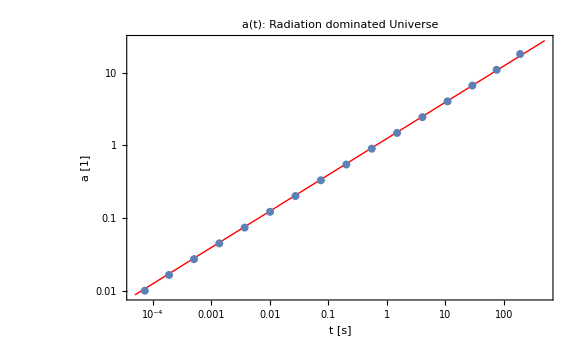

```mathematica
Show[LogLogPlot[atfitcurve, {t, 0.00005, 500}, PlotStyle -> {Red, Thick}], ListLogLogPlot[atdat[[;;160 ;; 10]], PlotStyle -> {PointSize[.01]}], PlotLabel -> Style[#, Bold, 15] & /@ {"a(t): Radiation dominated Universe"}, FrameLabel -> {"t [s]", "a [1]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, Epilog -> Inset[Style[Framed[Column[{PointLegend[{Blue}, {" Data"}], LineLegend[{Red}, {"Radiation: " @NumberForm[atfitcurve,4]}]}]], Bold, 12], Scaled[{0.98, 0.35}], Scaled[{1, 1}]], ImageSize -> Large]
```

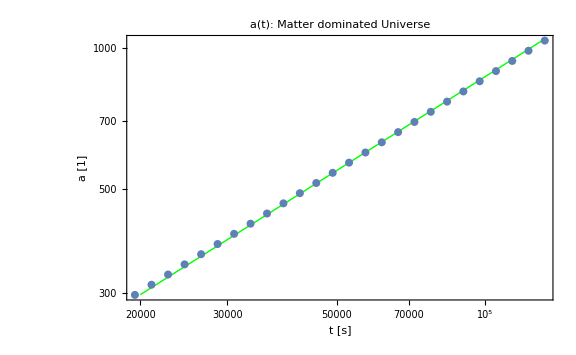

```mathematica
Show[LogLogPlot[atfitcurveCOLD, {t, 20000, 130000}, PlotStyle -> {Green, Thick}], ListLogLogPlot[atdat[[207;;]], PlotStyle -> {PointSize[.01]}], PlotLabel -> Style[#, Bold, 15] & /@ {"a(t): Matter dominated Universe"}, FrameLabel -> {"t [s]", "a [1]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, Epilog -> Inset[Style[Framed[Column[{PointLegend[{Blue}, {" Data"}], LineLegend[{Green}, {"Matter: " @NumberForm[atfitcurveCOLD,4]}]}]], Bold, 12], Scaled[{0.98, 0.3}], Scaled[{1, 1}]], ImageSize -> Large]
```

### Massive electrons

```mathematica
ρtott=Transpose[{tdat,(ργ+ρMassiveEl)*10^24}];
```

```mathematica
ρtottFunc=Interpolation[ρtott];
```

```mathematica
ρtota=Transpose[{adat,(ργ+ρMassiveEl)}];
ρtotaMassless=Transpose[{adat,(ργ+ρMasslessEl)}];
```

```mathematica
ρtotaFunc=Interpolation[ρtota];
ρtotaMasslessFunc=Interpolation[ρtotaMassless];
```

```mathematica
aTime=NDSolve[{((D[a[t],t]MevToSec)/a[t])^2==(8π)/3 G ρtotaFunc[a[t]],a[t0]==0.01},a,{t,t0,1000}]
```

NDSolve[{(4.33243×10^-43 a'[t]^2)/a[t]^2==5.62019×10^-44 Interpolation[Transpose[{{0.0100000000000000002,0.0105127109637602415,0.0110517091807564791,0.0116183424272828344,0.0122140275816017031,0.0128402541668774205,0.0134985880757600377,0.0141906754859325805,0.0149182469764127124,0.0156831218549016993,0.0164872127070012919,0.0173325301786739668,0.0182211880039051047,0.0191554082901389776,0.0201375270747047828,0.0211700001661267664,0.0222554092849246987,0.0233964685192599338,0.0245960311115695253,0.0258570965931584941,0.027182818284590491,0.0285765111806316786,0.0300416602394643767,0.0315819290968977276,0.0332011692273655248,0.0349034295746184706,0.0366929666761924983,0.0385742553069698124,0.040551999668446817,0.0426311451516882545,0.0448168907033807337,0.0471147018259075109,0.0495303242439512487,0.052069798271798598,0.0547394739172721162,0.0575460267600574338,0.0604964746441295984,0.0635981952260184641,0.0668589444227928598,0.0702868758058931009,0.0738905609893067,0.0776790110630679181,0.0816616991256767233,0.0858485839717791771,0.0902501349943414799,0.0948773583635855455,0.0997418245481475202,0.104855697247276072,0.110231763806416375,0.115883467192234274,0.121824939607035138,0.128071037826630735,0.134637380350017349,0.141540386453758493,0.148797317248728855,0.156426318841882267,0.164446467710971073,0.172877818405677008,0.18174145369443126,0.191059537282317171,0.200855369231877412,0.211153444225406939,0.22197951281441719,0.233360645809428058,0.245325301971094451,0.257903399171931613,0.271126389206579999,0.285027336437673973,0.299641000473971408,0.315003923087480653,0.331154519586924601,0.348133174876021745,0.365982344436781515,0.384746660490322967,0.404473043600675764,0.425210820000629763,0.447011844933010327,0.469930632315795016,0.494024491055304049,0.519353668348316866,0.545981500331445102,0.573974570454464761,0.603402875973622632,0.634340002981236384,0.666863310409254728,0.701054123466882118,0.736997936995961833,0.774784629252612711,0.814508686649685676,0.856269440022010442,0.900171313005223128,0.946324083149246098,0.994843156419343622,1.04584985577114797,1.09947172452124131,1.15584284527188319,1.21510417518735592,1.27740389846029623,1.34289779684936295,1.41174963921477703,1.48413159102577508,1.56022464486395962,1.64021907299902781,1.72431490316855385,1.81272241875152362,1.90566268458631249,2.00336809974792995,2.10608297866675853,2.21406416204188572,2.32758165907663628,2.44691932264222078,2.57237555905776549,2.70426407426154514,2.8429146582392284,2.98867400967062347,3.14190660285696444,3.3029955990965103,3.47234380478737092,3.65037467865331466,3.83753339061114707,4.0342879349273808,4.24113030044767481,4.45857770082520322,4.68717386782420409,4.92749041093260054,5.18012824668346017,5.4457191012593329,5.72492709013675594,6.01845037872086852,6.32702292812258538,6.65141633044367175,6.99244173815891035,7.35095189241978986,7.72784325535156214,8.12405825167549978,8.54058762526158688,8.97847291650425383,9.43880906671586573,9.9227471560503453,10.4314972818031215,10.9663315842846831,11.5285874278339815,12.1196707449258767,12.7410595517346508,13.3943076439443001,14.0810484820470858,14.8029992758455897,15.5619652783716838,16.3598442999594198,17.1986314537593898,18.0804241445608085,19.0074273133959792,19.9819589510413778,21.0064558942019772,22.0834799188723103,23.215724146110805,24.4060197762452447,25.657343168348266,26.9728232826853755,28.355749504745404,29.809579870417604,31.3379497128825761,32.9446807528387708,34.6337906547949146,36.409503073323954,38.2762582143994905,40.2387239382235507,42.3018074313084327,44.4706674769990613,46.7507273551183999,49.1476884029919034,51.667544271760498,54.3165959136304224,57.1014673375357234,60.0291221726109185,63.1068810808909788,66.3424400627796302,69.743889701059004,73.3197353915607977,77.0789186110860953,81.0308392757548148,85.185379245692161,89.5529270348262116,94.1444037875838404,98.9712905874403788,104.045657165608532,109.38019208165322,114.988234451499693,120.883807302171391,127.081652636661744,133.597268296620427,140.446946715030009,147.64781565577465,155.21788104197131,163.176071980156479,171.542288092912116,180.337449278287522,189.583548020440958,199.303704382305568,209.52222381778941,220.26465794807018,231.557868453957667,243.430094244087257,255.911022066900472,269.031860742979347,282.825419203353761,297.326188528918351,312.570428196100409,328.596256744437824,345.443747092782587,363.155026742471534,381.774383118022456,401.34837430876371,421.925945488308912,443.558551302985109,466.300284535250057,490.208011363824369,515.341513558758152,541.763637966995361,569.540453662226582,598.741417151987093,629.43954605510396,661.711601683776053,695.63828098683814,731.304418334166144,768.79919764678948,808.216375403147936,849.654515079123598,893.217233608069364,939.013460477114336,987.157710107620346,1037.77036820088347},ρMassiveEl+ργ}]][a[t]],a[0.0000738256]==0.01},a,{t,0.0000738256,1000}]

```mathematica
aTimeMassless=NDSolve[{((D[a[t],t]MevToSec)/a[t])^2==(8π)/3 G ρtotaMasslessFunc[a[t]],a[t0]==0.01},a,{t,t0,1000}]
```

NDSolve[{(4.33243×10^-43 a'[t]^2)/a[t]^2==5.62019×10^-44 Interpolation[Transpose[{{0.0100000000000000002,0.0105127109637602415,0.0110517091807564791,0.0116183424272828344,0.0122140275816017031,0.0128402541668774205,0.0134985880757600377,0.0141906754859325805,0.0149182469764127124,0.0156831218549016993,0.0164872127070012919,0.0173325301786739668,0.0182211880039051047,0.0191554082901389776,0.0201375270747047828,0.0211700001661267664,0.0222554092849246987,0.0233964685192599338,0.0245960311115695253,0.0258570965931584941,0.027182818284590491,0.0285765111806316786,0.0300416602394643767,0.0315819290968977276,0.0332011692273655248,0.0349034295746184706,0.0366929666761924983,0.0385742553069698124,0.040551999668446817,0.0426311451516882545,0.0448168907033807337,0.0471147018259075109,0.0495303242439512487,0.052069798271798598,0.0547394739172721162,0.0575460267600574338,0.0604964746441295984,0.0635981952260184641,0.0668589444227928598,0.0702868758058931009,0.0738905609893067,0.0776790110630679181,0.0816616991256767233,0.0858485839717791771,0.0902501349943414799,0.0948773583635855455,0.0997418245481475202,0.104855697247276072,0.110231763806416375,0.115883467192234274,0.121824939607035138,0.128071037826630735,0.134637380350017349,0.141540386453758493,0.148797317248728855,0.156426318841882267,0.164446467710971073,0.172877818405677008,0.18174145369443126,0.191059537282317171,0.200855369231877412,0.211153444225406939,0.22197951281441719,0.233360645809428058,0.245325301971094451,0.257903399171931613,0.271126389206579999,0.285027336437673973,0.299641000473971408,0.315003923087480653,0.331154519586924601,0.348133174876021745,0.365982344436781515,0.384746660490322967,0.404473043600675764,0.425210820000629763,0.447011844933010327,0.469930632315795016,0.494024491055304049,0.519353668348316866,0.545981500331445102,0.573974570454464761,0.603402875973622632,0.634340002981236384,0.666863310409254728,0.701054123466882118,0.736997936995961833,0.774784629252612711,0.814508686649685676,0.856269440022010442,0.900171313005223128,0.946324083149246098,0.994843156419343622,1.04584985577114797,1.09947172452124131,1.15584284527188319,1.21510417518735592,1.27740389846029623,1.34289779684936295,1.41174963921477703,1.48413159102577508,1.56022464486395962,1.64021907299902781,1.72431490316855385,1.81272241875152362,1.90566268458631249,2.00336809974792995,2.10608297866675853,2.21406416204188572,2.32758165907663628,2.44691932264222078,2.57237555905776549,2.70426407426154514,2.8429146582392284,2.98867400967062347,3.14190660285696444,3.3029955990965103,3.47234380478737092,3.65037467865331466,3.83753339061114707,4.0342879349273808,4.24113030044767481,4.45857770082520322,4.68717386782420409,4.92749041093260054,5.18012824668346017,5.4457191012593329,5.72492709013675594,6.01845037872086852,6.32702292812258538,6.65141633044367175,6.99244173815891035,7.35095189241978986,7.72784325535156214,8.12405825167549978,8.54058762526158688,8.97847291650425383,9.43880906671586573,9.9227471560503453,10.4314972818031215,10.9663315842846831,11.5285874278339815,12.1196707449258767,12.7410595517346508,13.3943076439443001,14.0810484820470858,14.8029992758455897,15.5619652783716838,16.3598442999594198,17.1986314537593898,18.0804241445608085,19.0074273133959792,19.9819589510413778,21.0064558942019772,22.0834799188723103,23.215724146110805,24.4060197762452447,25.657343168348266,26.9728232826853755,28.355749504745404,29.809579870417604,31.3379497128825761,32.9446807528387708,34.6337906547949146,36.409503073323954,38.2762582143994905,40.2387239382235507,42.3018074313084327,44.4706674769990613,46.7507273551183999,49.1476884029919034,51.667544271760498,54.3165959136304224,57.1014673375357234,60.0291221726109185,63.1068810808909788,66.3424400627796302,69.743889701059004,73.3197353915607977,77.0789186110860953,81.0308392757548148,85.185379245692161,89.5529270348262116,94.1444037875838404,98.9712905874403788,104.045657165608532,109.38019208165322,114.988234451499693,120.883807302171391,127.081652636661744,133.597268296620427,140.446946715030009,147.64781565577465,155.21788104197131,163.176071980156479,171.542288092912116,180.337449278287522,189.583548020440958,199.303704382305568,209.52222381778941,220.26465794807018,231.557868453957667,243.430094244087257,255.911022066900472,269.031860742979347,282.825419203353761,297.326188528918351,312.570428196100409,328.596256744437824,345.443747092782587,363.155026742471534,381.774383118022456,401.34837430876371,421.925945488308912,443.558551302985109,466.300284535250057,490.208011363824369,515.341513558758152,541.763637966995361,569.540453662226582,598.741417151987093,629.43954605510396,661.711601683776053,695.63828098683814,731.304418334166144,768.79919764678948,808.216375403147936,849.654515079123598,893.217233608069364,939.013460477114336,987.157710107620346,1037.77036820088347},ρMasslessEl+ργ}]][a[t]],a[0.0000738256]==0.01},a,{t,0.0000738256,1000}]

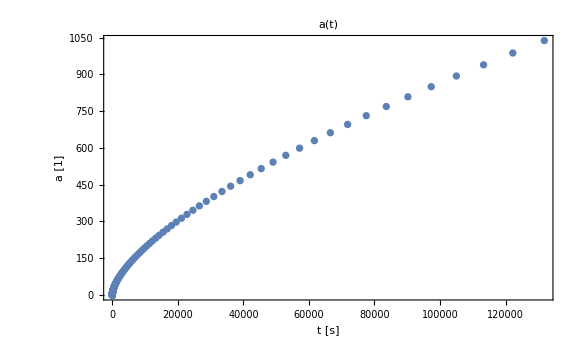

```mathematica
Show[Plot[Evaluate[a[t]/.aTime[[2]]],{t,t0,120},PlotStyle->{Green,Thick}],Plot[Evaluate[a[t]/.aTimeMassless[[2]]],{t,t0,120},PlotStyle->{Red,Thick}],ListPlot[atdat,PlotRange->{{t0,20},Automatic}],PlotLabel->Style[#,Bold,15]&/@{"a(t)"},Frame-> True, FrameLabel->{"t [s]","a [1]"},Axes->  None,Epilog->Inset[Style[Framed[Column[{PointLegend[{Blue},{" Data"}],LineLegend[{Red},{" Calculated for massless e" }],LineLegend[{Green},{" Calculated for massive e" }]}]],Bold,10],Scaled[{0.98,0.38}],Scaled[{1,1}]], ImageSize-> Large]
```

## Scale factor from temperature

### Solution of Friedmann Equation for massive electron

```mathematica
gLowEnergy=2;
```

```mathematica
ρtot=(ργ+ρMassiveEl)*10^24;
```

```mathematica
ρtotTFunc=Interpolation[ρtotT];
```

```mathematica
Plot[ρtotTFunc[T],{T,0,100}]
```

-Graphics-

```mathematica
aTemp=NDSolve[{(a'[T]/a[T])^2((T)^3/(Mpl MevToSec))^2==(8π)/3 G ρtotTFunc[T],a[9.983111*10^-3]==140.3066},a,{T,1,100}]
```

NDSolve[{(0.458697 T^6 a'[T]^2)/a[T]^2==5.62019×10^-44 Interpolation[ρtotT][T],a[0.00998311]==140.307},a,{T,1,100}]

```mathematica
aTemp[[1,2]]
```

a[0.00998311]==140.307

```mathematica
LogLinearPlot[Evaluate[{Re[ a[T]]}/.aTemp[[1]]],{T,1,100},PlotRange->All]
```

-Graphics-

```mathematica
Evaluate[{Re[a[50]]}/.aTemp[[1]]]
```

{Re[a[50]]}/.{(0.458697 T^6 a'[T]^2)/a[T]^2==5.62019×10^-44 Interpolation[ρtotT][T],a[0.00998311]==140.307}

```mathematica
aTempdat=Transpose[{Tdat,adat}];
```

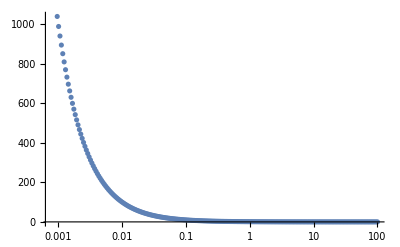

```mathematica
ListLogLinearPlot[aTempdat,PlotRange->All]
```

## a*T

```mathematica
adat*Tdat;
```

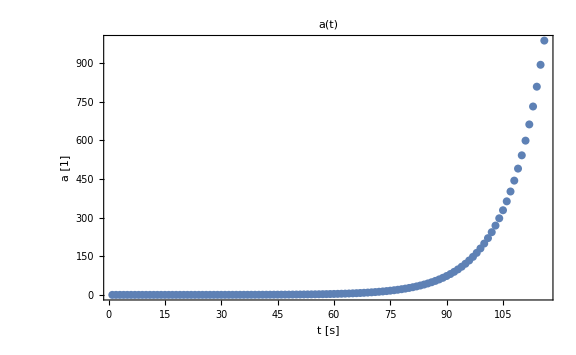

```mathematica
Show[ListPlot[adat[[;; ;; 2]], PlotStyle -> {PointSize[.01]}], PlotLabel -> Style[#, Bold, 15] & /@ {"a(t)"}, FrameLabel -> {"t [s]", "a [1]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, ImageSize -> Large]
```

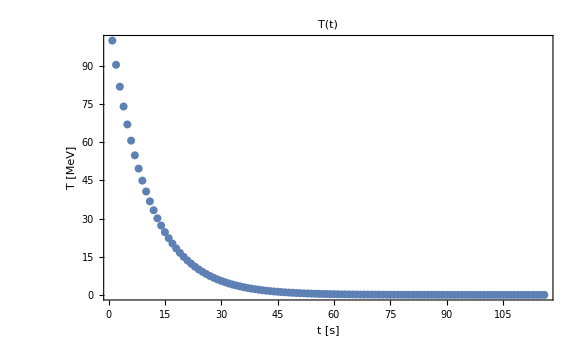

```mathematica
Show[ListPlot[Tdat[[;; ;; 2]], PlotStyle -> {PointSize[.01]}], PlotLabel -> Style[#, Bold, 15] & /@ {"T(t)"}, FrameLabel -> {"t [s]", "T [MeV]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, ImageSize -> Large]
```

```mathematica
aTT = Transpose[{Tdat, aTdat}];
```

```mathematica
aTt
```

aTt

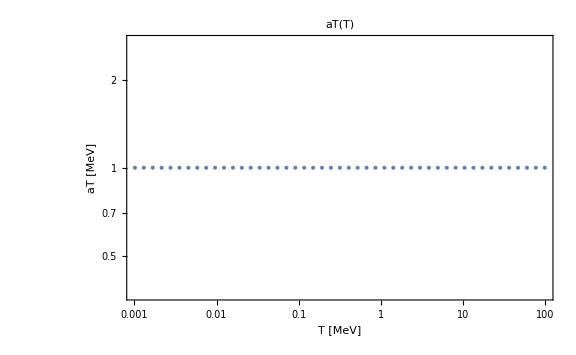

```mathematica
Show[ListLogLogPlot[aTT[[;; ;; 5]], PlotStyle -> {PointSize[.005]}], PlotLabel -> Style[#, Bold, 15] & /@ {"aT(T)"}, FrameLabel -> {"T [MeV]", "aT [MeV]"}, PlotRange -> All, AxesOrigin -> {0, 0}, Axes -> False, Frame -> True, ImageSize -> Large]
```

```mathematica
Export["/home/stasya/Desktop/Link to 2master/1BBN/test_results/photon-electron_universe/photon-electron-aTT.png",%148,"PNG"]
```

$Failed

```mathematica
s
```

s

aT is not conserving, starting from the temperature [MeV] (t=15 s):

```mathematica
TaT=√(Mpl/(2 15)MevToSec)
```

0.221849

## Dof from time

ρ=ρ(photons)+ρ(relativistic fermions)
Neff - number of relativistic fermions
Neff=(ρ-π^2/15 T^4)/(7/8 π^2/15 (T/1.4)^4) (

```mathematica
Nefftdat=Transpose[{tdat,Neffdat}];
```

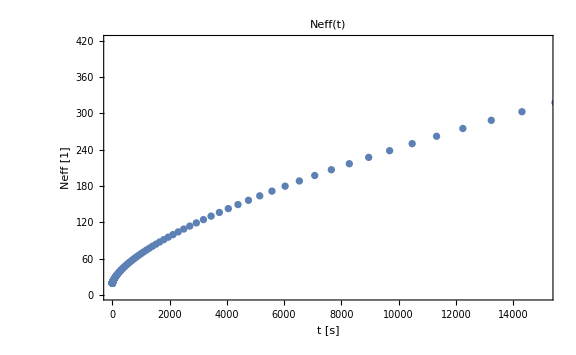

```mathematica
Show[ListPlot[Nefftdat],PlotLabel->Style[#,Bold,15]&/@{"Neff(t)"},Frame-> True, FrameLabel->{"t [s]","Neff [1]"},ImageSize-> Large]
```